# 2 Dimensions

First, define the numerics to have some feduciary point

```mathematica
Ψ[n_,x_,m_,y_,L_]:= 1/L*Exp[-ⅈ*2 π/L(n*x+y*m)]
```

```mathematica
Hp[n_,x_,m_,y_,L_,Φ_,V_,c_] := (-1/2(D[D[Φ[n,q,m,y,L],q],q]+D[D[Φ[n,x,m,w,L],w],w])-V*Exp[(-2(x^2+y^2))/c^2]Φ[n,x,m,y,L])/.{q->x,w->y}
```

```mathematica
Clear[Hp]
```

```mathematica
Conjugate[Ψ[1,x,1,y,10]]
```

1/10 ⅇ^(1/5 ⅈ π Conjugate[x+y])

```mathematica
Hp[2,1,2,1,10,Ψ,1.5,1]
```

-0.0831117-0.0603842 ⅈ

```mathematica
Conjugate[Ψ[1,x,1,y,10]]*Hp[2,x,2,y,10,Ψ,1.5,1]
```

1/10 ⅇ^(1/5 ⅈ π Conjugate[x+y]) (-0.15 ⅇ^(-1/5 ⅈ π (2 x+2 y)+1/2 (-x^2-y^2))+2/125 ⅇ^(-1/5 ⅈ π (2 x+2 y)) π^2)

```mathematica
Hp[2,2,2,2,10,Ψ,1.5,1]
```

0.047949+0.147572 ⅈ

```mathematica
NIntegrate[NIntegrate[Conjugate[Ψ[1,x,1,y,10]]*Hp[2,x,2,y,10,Ψ,1.5,1],{x,-10/2,10/2}],{y,-10/2,10/2}]//Chop//Quiet
```

-0.0635066

```mathematica
-1/2(D[D[Ψ[n,x,m,y,L],x],x])
```

-(2 ⅇ^((2 π (n x+m y))/L) n^2 π^2)/L^3

```mathematica
HM[V_,L_]:= Table[NIntegrate[NIntegrate[Conjugate[Ψ[n,x,m,y,L]]*Hp[l,x,q,y,L,Ψ,V,1],{x,-10/2,10/2}],{y,-10/2,10/2}]//Chop//Quiet,{n,-5,5},{m,-5,5},{l,-5,5},{q,-15,15}]
```

```mathematica
HM[1.5,10]
```

$Aborted

```mathematica
HPlane[V_,L_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[(-(2*π/L)^2(n-l)^2)/8]*π*1/(2*L^2)Exp[(-(2*π/L)^2(m-q)^2)/8]
```

```mathematica
H2Plane[V_,L_,b_,n_,m_,l_,q_]:= KroneckerDelta[n,l]*KroneckerDelta[m,q]*(2*π/L)^2(n^2+m^2)/2- V*Exp[((b+ⅈ*4(2*π/L)(n-l))^2-b^2)/8]*π*1/(2*L^2)Exp[(ⅈ*4(2*π/L)(m-q))^2/8]-V*Exp[((-b+ⅈ*4(2*π/L)(n-l))^2-b^2)/8]*π*1/(2*L^2)Exp[(ⅈ*4(2*π/L)(m-q))^2/8]
```

```mathematica
NIntegrate[NIntegrate[Conjugate[Ψ[1,x,1,y,10]]*Hp[2,x,2,y,10,Ψ,1.5,1],{x,-10/2,10/2}],{y,-10/2,10/2}]//Chop//Quiet
```

-0.0213475

```mathematica
NIntegrate[NIntegrate[Conjugate[Ψ[1,x,1,y,10]]*Hp[2,x,2,y,10,Ψ,1.5,1],{x,-10/2,10/2}],{y,-10/2,10/2}]//Chop//Quiet
```

$Aborted

```mathematica
HPlane[1.5,10,1,1,2,2]
```

-0.0213475

```mathematica
Test=Table[{x,y,z},{x,-1,1},{y,-2,0},{z,0,2}]
```

{{{{-1,-2,0},{-1,-2,1},{-1,-2,2}},{{-1,-1,0},{-1,-1,1},{-1,-1,2}},{{-1,0,0},{-1,0,1},{-1,0,2}}},{{{0,-2,0},{0,-2,1},{0,-2,2}},{{0,-1,0},{0,-1,1},{0,-1,2}},{{0,0,0},{0,0,1},{0,0,2}}},{{{1,-2,0},{1,-2,1},{1,-2,2}},{{1,-1,0},{1,-1,1},{1,-1,2}},{{1,0,0},{1,0,1},{1,0,2}}}}

```mathematica
TestMatrix = Table[x1*y1*x2*y2,{x1,{m1,m2}},{y1,{n1,n2}},{x2,{l1,l2}},{y2,{q1,q2}}]//MatrixForm
```

((l1 m1 n1 q1 | l1 m1 n1 q2
l2 m1 n1 q1 | l2 m1 n1 q2) | (l1 m1 n2 q1 | l1 m1 n2 q2
l2 m1 n2 q1 | l2 m1 n2 q2)
(l1 m2 n1 q1 | l1 m2 n1 q2
l2 m2 n1 q1 | l2 m2 n1 q2) | (l1 m2 n2 q1 | l1 m2 n2 q2
l2 m2 n2 q1 | l2 m2 n2 q2))

```mathematica
HMatrix=Table[HPlane[1.5,12,m,l,n,q],{m,-9,9},{n,-9,9},{l,-9,9},{q,-9,9}];
```

```mathematica
EM1=Eigensystem[ArrayFlatten[HMatrix]-100IdentityMatrix[17^2]];
```

```mathematica
groundState[EM_,L_,x_,y_]:= Module[{i,j},Sum[Normalize[EM][[(i-1)*19+j]]*Exp[-ⅈ*2*π/L*((i-10)*x+(j-10)*y)]/L,{i,1,19},{j,1,19}]]
```

```mathematica
Clear[groundState]
```

```mathematica
Plot3D[-1.5Exp[-2*x^2-2*y^2],{x,-1.5,1.5},{y,-1.5,1.5},PlotRange->{0,-1.5}]
```

-Graphics3D-

```mathematica
groundState[EM1[[2]][[1]],10,2,0]
```

-0.0410527+0.126347 ⅈ

```mathematica
Plot3D[Abs[groundState[EM1[[2]][[2]],10,x,y]]^2,{x,-5,5},{y,-5,5},PlotRange->{0,.2}]
```

-Graphics3D-

```mathematica
GroundStatePlane[p_,l_]:= Module[{HMatrix,EN,G,m,k,n,q},
HMatrix=Table[HPlane[1.5,10,m,l,n,q],{m,-p,p},{n,-p,p},{k,-p,p},{q,-p,p}];
EN = Eigensystem[ArrayFlatten[HMatrix]-100*IdentityMatrix[(2*p+1)^2]];
G = {EN[[1]][[1]]+100,EN[[2]][[1]]}]
```

```mathematica
Clear[l]
```

```mathematica
GroundStatePlane[6,7][[1]]
```

-0.549367

```mathematica
Table[{l,GroundStatePlane[9,l][[1]]},{l,6,16}]
```

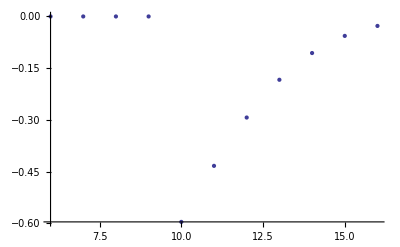

```mathematica
ListPlot[{{6,-5.542233338928781*^-13},{7,-6.110667527536862*^-13},{8,-4.121147867408581*^-13},{9,-4.689582056016661*^-13},{10,-0.5957323274620734},{11,-0.43322760049343856},{12,-0.2930846429748044},{13,-0.18358482169735169},{14,-0.10606863593476135},{15,-0.05635125618836412},{16,-0.02746036611623026}}]
```

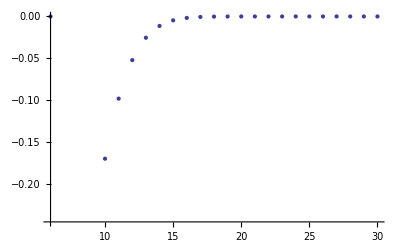

```mathematica
ListPlot[{{6,-2.1316282072803006*^-13},{7,-0.5493671221744592},{8,-0.3995163567906559},{9,-0.27027990505342814},{10,-0.169300474421064},{11,-0.09781570861223088},{12,-0.05196671804816333},{13,-0.025323750795436695},{14,-0.011296512736734599},{15,-0.004605396533776229},{16,-0.001713639352573182},{17,-0.0005813382655333044},{18,-0.00017964099799883115},{19,-0.00005052719193088251},{20,-0.000012927581650501452},{21,-3.007143590139094*^-6},{22,-6.356866606438416*^-7},{23,-1.220731036255529*^-7},{24,-2.1288556695253646*^-8},{25,-3.3705447322063264*^-9},{26,-4.843911938223755*^-10},{27,-6.31388274996425*^-11},{28,-7.418066161335446*^-12},{29,-8.100187187665142*^-13},{30,-2.8421709430404007*^-13}}]
```

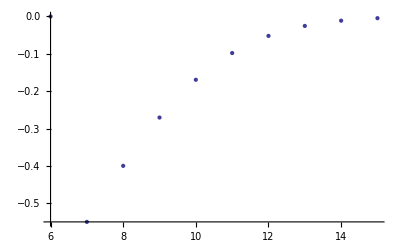

```mathematica
ListPlot[{{6,-2.1316282072803006*^-13},{7,-0.5493671221744592},{8,-0.3995163567906559},{9,-0.27027990505342814},{10,-0.169300474421064},{11,-0.09781570861223088},{12,-0.05196671804816333},{13,-0.025323750795436695},{14,-0.011296512736734599},{15,-0.004605396533776229}}]
```

```mathematica
H2Matrix=Table[H2Plane[1.5,10,1,m,l,n,q],{m,-9,9},{n,-9,9},{l,-9,9},{q,-9,9}];
```

```mathematica
ArrayFlatten[H2Matrix][[122]][[1]]
```

5.60259×10^-20+0. ⅈ

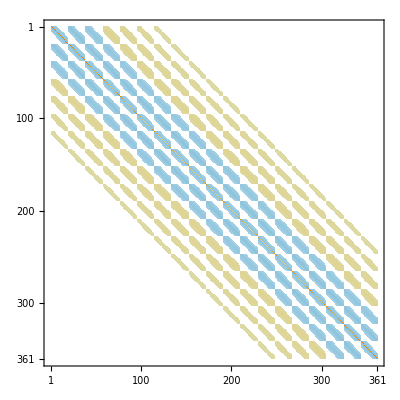

```mathematica
MatrixPlot[ArrayFlatten[H2Matrix]]
```

```mathematica
ArrayFlatten[HMatrix][[100]][[100]]
```

6.15214

```mathematica
EM2=Eigensystem[ArrayFlatten[H2Matrix]-100IdentityMatrix[19^2]]
```

{{-100.057,-99.866,-99.8545,-99.8516,-99.836,-99.6511,-99.6507,-99.6496,«345»,-71.4173,-71.4173,-71.4173,-71.4173,-68.0694,-68.0694,-68.0694,-68.0694},«1»}

```mathematica
Plot3D[Abs[groundState[EM2[[2]][[1]],10,x,y]]^2,{x,-5,5},{y,-5,5},PlotRange->{0,.05}]
```

-Graphics3D-

## Harmonic Oscillator

```mathematica
HMV1[l_,m_,ω_,b_,c_]:= (Sqrt[ω]/Sqrt[2^(l+m)Factorial[l]*Factorial[m]]*Sum[{2^k Factorial[k]*Binomial[l,k]*Binomial[m,k]*(1-2*(ω*c^2)/(1+2 c^2 ω))^((m+l)/2-k)*HermiteH[(m+l-2*k),Sqrt[ω/(1+2*c^2*ω)]*b]},{k,0,Min[m,l]}]*Exp[b^2/(2 c^2)(1/(1+2 c^2*ω)-1)]*Sqrt[2/(1+2 c^2*ω)]c)[[1]]
```

```mathematica
Hx2Anal2[l_,m_]:= 1/2(2*l+1)*KroneckerDelta[l,m]-1/2 Sqrt[(l+1)(l+2)]KroneckerDelta[l+1,m-1]-1/2 Sqrt[(m+1)(m+2)]KroneckerDelta[l-1,m+1]
```

```mathematica
HOBasis[V_,b_,c_,size_]:= Module[{ω=Sqrt[2*V/(2*b*c+9*c^2)]},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
HOBasis1Well[V_,c_,size_]:= Module[{ω=Sqrt[2*V/c^2]},Table[ω/2*Hx2Anal2[n,m]*KroneckerDelta[l,q]+ω/2*Hx2Anal2[l,q]*KroneckerDelta[m,n]-V*HMV1[n,m,ω,0,c]*HMV1[l,q,ω,0,c],{n,0,size-1},{l,0,size-1},{m,0,size-1},{q,0,size-1}]]
```

```mathematica
MHo = HOBasis1Well[1.5^2,.5,7];
```

```mathematica
Length[ArrayFlatten[MHo]]
```

49

```mathematica
Em=Eigensystem[ArrayFlatten[MHo]-1000*IdentityMatrix[49]];
```

```mathematica
plotGround[Ψ_,H_,V_,c_,b_,size_,]:= Module[{x,k,Em,M,HOBasis},

Plot[{Sum[k,{k,Table[Ψ[n,x,V,c]*Normalize[Em[[2]][[1]]][[n+1]], {n,0,size}]}],-V/(c*Sqrt[2π])Exp[-x^2/(4*V*c^2)]},{x,-10,10}]
]
```

```mathematica
plotGround
```

```mathematica
plotGround2wellHO2d[Ψ_,V_,b_,c_,size_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)],HOBasis},
HOBasis[V,b,c,size,ω]:= Module[{},Table[ω/2*Hx2Anal2[n,m]+ω/2*Hx2Anal2[l,q]-V*HMV1[n,m,ω,b,c]*HMV1[l,q,ω,0,c],{n,0,size},{l,0,size},{m,0,size},{q,0,size}]];
Em = Eigensystem[ArrayFlatten[HOBasis[1.5^2,1,.5,7,ω]-1000*IdentityMatrix[42]]]

Plot[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,x,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,17},{j,1,17}]]^2},{x,-3,3}]
]
```

```mathematica
plotGround2wellHO2dT[Ψ_,V_,b_,c_,size_,Em_]:= Module[{k,ω=Sqrt[2*V/(6b*c+9 c^2)]},
Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}];

Plot3D[{Abs[Sum[Ψ[i-1,x,V,c,ω]*Ψ[j-1,y,V,c,ω]*Normalize[Em[[2]][[1]]][[(i-1)*(size)+j]],{i,1,size},{j,1,size}]]^2},{x,-3,3},{y,-3,3}]
]
```

```mathematica
Ψ2p[n_,x_,V_,c_,w_] := Φ[n,x]/.{ω->w,h->1,m->1}
```

```mathematica
Ψ2p[0,10,1.5,.5,1]
```

1/(ⅇ^50 π^(1/4))

```mathematica
plotGround2wellHO2dT[Ψ2p,1.5^2,0,.5,7,Em]
```

-Graphics3D-

```mathematica
Clear[plotGround2wellHO2d]
```

```mathematica
Sum[Sin[j],{j,1,10}]
```

Sin[1]+Sin[2]+Sin[3]+Sin[4]+Sin[5]+Sin[6]+Sin[7]+Sin[8]+Sin[9]+Sin[10]